# Laborathory 2

Using of Mathematica Platform – the revision tasks

1. Solve  the  system  of  linear  equations

```mathematica
a ={{1,2,0},{-1,1,0},{0,1,2}};
b= Transpose[{3,1,3}];
LinearSolve[a,b]
```

{1/3,4/3,5/6}

2.  Solve  the  system  of  linear  equations  with  respect  to  respect  to  variable  z :

```mathematica
ClearAll[a,b,x,y,z]
a = {{1,-2,3},{2,3,-1}};
b = Transpose[{1,5}];
variables=Transpose[{x,y,z}];
solution=Solve[a.variables==b,{x,y}]
```

{{x→13/7-z,y→1/7 (3+7 z)}}

3.  Calculate :

a)

```mathematica
Limit[E^x/(x^3-x+2),x->Infinity]
```

∞

b)

```mathematica
Limit[E^(1/(x^2-1)),x->1,Direction->"FromAbove"]
```

∞

c)

```mathematica
Limit[E^(1/(x^2-1)),x->1,Direction->"FromBelow"]
```

0

d)

```mathematica
Integrate[Sin[x]/x,{x,0,Infinity}]
```

π/2

```mathematica
FullSimplify[D[x^3*Sin[x*y]/Cos[x^2+x*y],{x,2},{y,3}]]
```

1/2 x^4 Sec[x (x+y)]^6 (6 (15+86 x^4+88 x^3 y+22 x^2 y^2) Cos[x^2]-2 (-15+2 x^2 (73 x^2+62 x y+13 y^2)) Cos[x (x+2 y)]+15 (2 Cos[x (3 x+2 y)]-Cos[x (3 x+4 y)]-Cos[x (5 x+4 y)])+x (-4 x (33 x^2+42 x y+13 y^2) Cos[x (3 x+2 y)]+2 x (3 x+y)^2 Cos[x (3 x+4 y)]+2 x (x+y)^2 Cos[x (5 x+4 y)]-78 x Sin[x^2]+286 x Sin[x (x+2 y)]+120 y Sin[x (x+2 y)]+234 x Sin[x (3 x+2 y)]+120 y Sin[x (3 x+2 y)]-39 x Sin[x (3 x+4 y)]-12 y Sin[x (3 x+4 y)]-(13 x+12 y) Sin[x (5 x+4 y)]))

4. Solve  the  differential  equation  y ‘ = y·x .

```mathematica
ClearAll[y,x]
DSolve[y'[x]==x*y[x],y[x],x]
```

{{y[x]→ⅇ^(x^2/2) C[1]}}

5.  Solve  the  initial  problem . Find  the  numerical  value  of  the  solution  for  x = 7/2

```mathematica
sol=DSolve[{y'[x]==y[x]*x,y[1]==2},y[x],x]
f[x_]=y[x]/.sol[[1]];
f[7/2]
```

{{y[x]→2 ⅇ^(-1/2+x^2/2)}}

2 ⅇ^(45/8)

6.  Solve  the  partial  differential  equation with  initial  condition  y (0, t) = cos  t . Draw  the  graph  of  the  solution  for  x ∈ [0, 3] and  t ∈ [−1, 4] .

```mathematica
ClearAll[x,y,t];
equation=2*D[y[x,t],x]+D[y[x,t],t]==0;
sol=DSolve[{equation,y[0,t]==Cos[t]},y[x,t],{x,t}];
f[x_,t_]=y[x,t]/.sol[[1]];
Plot3D[f[x,t],{x,0,3},{t,-1,4}]
```

-Graphics3D-

7. By  using  the  summing  function  .1cnd  the  6 - element  approximation  of  the  exponential function  by  the  Maclaurin  series

```mathematica
aproximation[x_]=Sum[x^i/i!,{i,0,5}]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120

Calculate  the  values  of  the  obtained  approximation  for  x = 2.

```mathematica
aproximation[2]
```

109/15

Compare  in  one  figure  the  plots  of  the  exponential  function  and  the  obtained  6  element  approximation  (domain  of  the  plot : [−2, 7], range  of  the  plot : [0, 100], exponential  line  should  be  red  and  bold, approximating  line  should  be  black  and  dashed) .

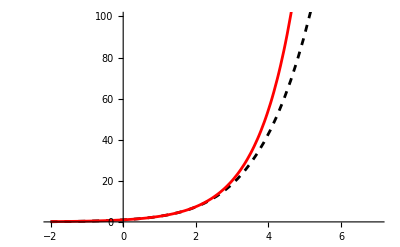

```mathematica
aproxPlot =Plot[aproximation[x],{x,-2,7},PlotStyle->{Dashed,Black}];
funcPlot = Plot[E^x,{x,-2,7},PlotStyle->{Bold,Red}];
Show[aproxPlot,funcPlot,PlotRange->{0,100}]
```

8. Investigate the function Graphics available in Mathematica. Draw a circle, disk,

arrow, line rectangle (of various sizes and colours) by using this function. Place

these objects in the system of coordinates.

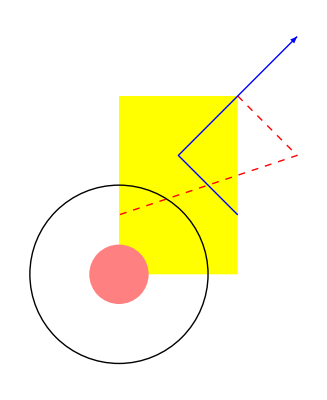

```mathematica
Graphics[{Yellow,Rectangle[{0,0},{2,3}],
Black,Circle[{0,0},1.5],{Thick,Dashed,Red,Line[{{2,3},{3,2},{0,1}}]},
Blue,Arrowheads[Large],Arrow[{{2,1},{1,2},{3,4}}],
Pink,Disk[{0,0},0.5]
}]
```

9. Define  the  conditional  function  (check  the  Piecewise  function  available  in  Mathematica) 
Draw  the  graph  of  this  function  in  domain [−2, 2]  (line  should  be  purple, the  units    should  be  equal, the  axes  should  be  removed  from  the  picture, the  picture  should    be  put  in  frame, the  proper  endings  of  the  line  should  be  respectively  marked  with   the  filled  or  empty  circles) .

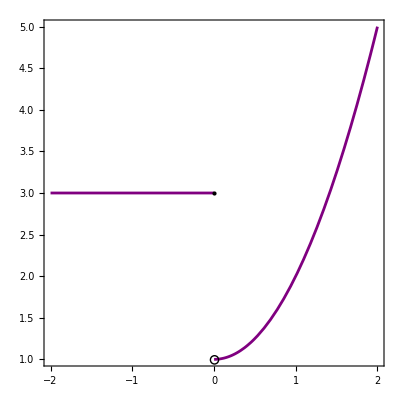

```mathematica
Clear[y,x]
y[x_]:=Piecewise[{{3,x<=0},{x^2+1,x>0}}]
plot=Plot[y[x],{x,-2,2},PlotStyle->Purple,Axes->False,Frame->True,AspectRatio->1];
endpoints=Graphics[{Black,PointSize[Large],Point[{0,y[0]}],
Black, Thick,Circle[{0,1},0.05]}
];
Show[plot,endpoints]
```